```mathematica
m[R_]:=-(η+ϵ-ϵ*R)+√((η+ϵ-ϵ*R)^2+4*R*ϵ*η)
```

```mathematica
n[R_]:=(((m[R]^2+4η*m[R]+2*ϵ*m[R]+4η^2+4*ϵ*η+4η)^2-4*(2*m[R]^3+12*η*m[R]^2+24*η^2*m[R]+8*ϵ*η*m[R]+16*η^3+16*ϵ*η^2)))/4(m[R]+2η)
```

```mathematica
ϵ=0.01
```

0.01

```mathematica
R=4.5
```

4.5

```mathematica
η=1
```

1

```mathematica
Clear[R,ϵ,η]
```

```mathematica
Solve[n[R]==0,R]
```

{{R→-100. (-1.00495+1. η)-0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))-0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)-0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)-(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-1. (4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-(0.25 (-6.4×10^7 (-1.00495+1. η)^3+9.6×10^7 (-1.00495+1. η) (0.019883-1.66987 η+1. η^2)-8. (-1184.04+58006. η-7.979×10^6 η^2+4.×10^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))))},{R→-100. (-1.00495+1. η)-0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))+0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)-0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)-(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-1. (4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-(0.25 (-6.4×10^7 (-1.00495+1. η)^3+9.6×10^7 (-1.00495+1. η) (0.019883-1.66987 η+1. η^2)-8. (-1184.04+58006. η-7.979×10^6 η^2+4.×10^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))))},{R→-100. (-1.00495+1. η)+0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))-0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)-0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)-(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-1. (4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(0.25 (-6.4×10^7 (-1.00495+1. η)^3+9.6×10^7 (-1.00495+1. η) (0.019883-1.66987 η+1. η^2)-8. (-1184.04+58006. η-7.979×10^6 η^2+4.×10^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))))},{R→-100. (-1.00495+1. η)+0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))+0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)-0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)-(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)-1. (4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(0.25 (-6.4×10^7 (-1.00495+1. η)^3+9.6×10^7 (-1.00495+1. η) (0.019883-1.66987 η+1. η^2)-8. (-1184.04+58006. η-7.979×10^6 η^2+4.×10^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883-1.66987 η+1. η^2)+0.0000333333 (1.19298×10^7-1.00192×10^9 η+6.×10^8 η^2)+(1.11111×10^-9 (2.48014×10^9-1.67221×10^16 η+1.66497×10^17 η^2))/(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3)+(4.57457-2.02457×10^8 η+8.0623×10^12 η^2-2.5162×10^12 η^3+1.85185×10^-14 √(0.-4.16703×10^36 η+1.11417×10^44 η^2+9.18453×10^48 η^3+1.88986×10^53 η^4-1.12747×10^53 η^5))^(1/3))))}}

```mathematica
p[η_]:=-100. (-1.00495+1. η)+0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)+0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)+(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3))-0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)-0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)-(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)-1. (4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(0.25 (-6.4*^7 (-1.00495+1. η)^3+9.6*^7 (-1.00495+1. η) (0.019883001666666667-1.6698666666666666 η+1. η^2)-8. (-1184.04+58006. η-7.979*^6 η^2+4.*^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)+0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)+(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3))))
```

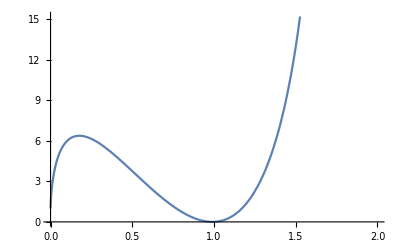

```mathematica
Plot[p[η],{η,0,2}]
```

```mathematica
q[η_]:=-100. (-1.00495+1. η)+0.5 √(40000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)+0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)+(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3))+0.5 √(80000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)-0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)-(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)-1. (4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(0.25 (-6.4*^7 (-1.00495+1. η)^3+9.6*^7 (-1.00495+1. η) (0.019883001666666667-1.6698666666666666 η+1. η^2)-8. (-1184.04+58006. η-7.979*^6 η^2+4.*^6 η^3)))/(√(40000. (-1.00495+1. η)^2-60000. (0.019883001666666667-1.6698666666666666 η+1. η^2)+0.000033333333333333335 (1.1929801*^7-1.00192*^9 η+6.*^8 η^2)+(1.111111111111111*^-9 (2.480139601*^9-1.672205767184*^16 η+1.664966416*^17 η^2))/(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3)+(4.57457156553337-2.0245716088196132*^8 η+8.062301670588214*^12 η^2-2.5161959125357036*^12 η^3+1.8518518518518517*^-14 √(0.-4.1670275564506855*^36 η+1.1141654498403899*^44 η^2+9.184532410968864*^48 η^3+1.889863514130387*^53 η^4-1.1274722718045875*^53 η^5))^(1/3))))
```

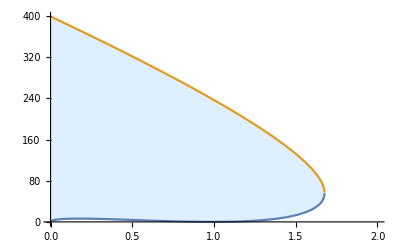

```mathematica
Plot[{p[η],q[η]},{η,0,2},Filling->{1->{{2},{LightBlue,White}}}]
```

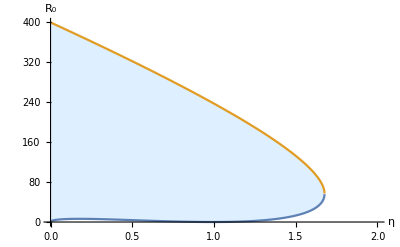

```mathematica
Show[%17,AxesLabel->{HoldForm[η],HoldForm[Subscript[R, 0]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Desktop\\0.01.pdf",%18,"PDF"]
```

C:\Users\Roger Zhang\Desktop\0.01.pdf